# Fast introduction

## Graphics

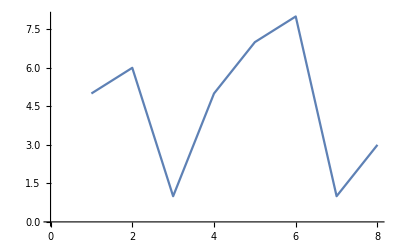

```mathematica
ListLinePlot[{5,6,1,5,7,8,1,3}]
```

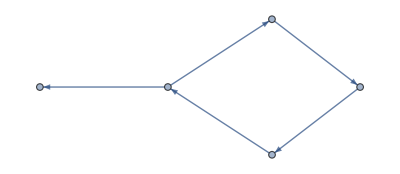

```mathematica
Graph[{1->3,1->2,2->4,4->5,5->1}]
```

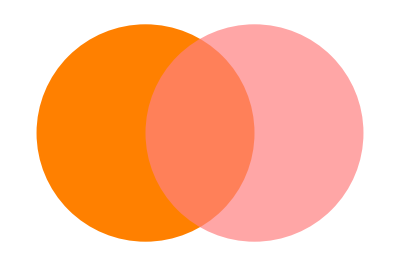

```mathematica
Graphics[{Orange,Disk[{0,0}], Opacity[.7],Pink,Disk[{1,0}]}]
```

### Interactive interfaces

```mathematica
Manipulate[Plot[Sin[a x],{x,0,10}],{a,5,10}]
```

```mathematica
Manipulate[Range[n],{n,1,50,3}]
```

```mathematica
TabView[{
Plot[Cos[2x], {x,0,10Pi}],Plot[Sin[x],{x,0,10 Pi}], "You expected next plot, aren't you?"
}]
```

123

```mathematica
Button[
"DO NOT TOUCH SANDVICH!",Import["http://orig02.deviantart.net/1e6d/f/2013/013/8/6/team_fortress_2_heavy_and_sandvich_wallpaper_by_dunkmovies-d5rg8li.jpg"
]
] 
(*Here is a bug with image showing*)
```

DO NOT TOUCH SANDVICH!

```mathematica
Slider[Dynamic[x]]
```

```mathematica
x
```

0.7

### Procedures

```mathematica
Print[a]; Print[b]; Print[c]
```

a

b

c

```mathematica
Module[{a=1},a+8]
```

9

```mathematica
7 > 5
```

True

```mathematica
If[
	7>5 && 2 ≤ 4,a,b
]
```

a

```mathematica
a=1;b=2;If[a > b, False, True]
a=1;b=2;If[a < b, False, True]
a=1;b=2;a<b
```

True

False

True

```mathematica
a=0;Module[{a=1},a+1];a
```

0